## Chapter 4 Algebra

### Section 4.1

Using a Plot we can see the function appears to have two real roots.

```mathematica
Clear[f];
f[x_]:=1+5x+2 x^3+10 x^4
```

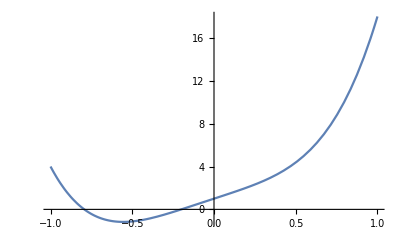

```mathematica
Plot[f[x],{x,-1,1}]
```

The exact values of the two real roots are x=-1/5 and x=-(1/2)^(1/3).

```mathematica
Factor[f[x]]
```

(1+5 x) (1+2 x^3)

```mathematica
Clear[f]
```

Mathematica can factor general forms of polynomials but the result may not always match the full factorization you get for every polynomial with numeric exponents.

This is an example where the general expression can be factored but when n=1 and m=3 we get a different factorization. Part b helps to clarify this result.

```mathematica
Clear[x,m,n];
Factor[1+x^n+x^m+x^(n+m)]
```

(1+x^m) (1+x^n)

```mathematica
Factor[1+x+x^3+x^4]
```

(1+x)^2 (1-x+x^2)

1+x^n cannot be factored over the reals for all values of n. It can be factored if n is odd but not for n even. The result below explains the connection between the two factorizations above, 1+x+x^3+x^4=(1+x)(1+x^3)=(1+x)(1+x)(1-x+x^2)=(1+x)^2(1-x+x^2)

```mathematica
Factor[1+x^3]
```

(1+x) (1-x+x^2)

```mathematica
Factor[1+x^n]
```

1+x^n

These results also show the difference between the factorization of the general expression 1-x^(2n) and the specific case 1-x^4.

```mathematica
Factor[1-x^4]
```

-(-1+x) (1+x) (1+x^2)

```mathematica
Factor[1-x^(2n)]
```

-(-1+x^n) (1+x^n)

### Section 4.2

When we use Solve to find the roots, at first glance there appear to be four real roots.

```mathematica
Clear[f,x];
f[x_]:=1+5x+2 x^3+10 x^4
Solve[f[x]==0,x]
```

{{x→-1/5},{x→(-1/2)^(1/3)},{x→-1/2^(1/3)},{x→-(-1)^(2/3)/2^(1/3)}}

NSolve makes it clear that two of the roots are real while the other two are complex.

```mathematica
NSolve[f[x]==0,x]
```

{{x→-0.793701},{x→-0.2},{x→0.39685-0.687365 ⅈ},{x→0.39685+0.687365 ⅈ}}

```mathematica
Clear[f]
```

In version 12 and later the outputs look identical. Prior to version 12, the answers look very different, but they are essentially the same apart from issues of rounding. The imaginary parts of the complex numbers in the first output below are very small—at the threshold of machine precision for a nonzero number. NSolve recognizes this and Chops the imaginary parts to zero. In most cases both approaches will give the same output, but there are cases like this where NSolve gives the better solution.

```mathematica
N[Solve[x^3-15x+2==0,x]]
```

{{x→-3.938},{x→0.133492},{x→3.80451}}

```mathematica
NSolve[x^3-15x+2==0,x]
```

{{x→-3.938},{x→0.133492},{x→3.80451}}

There are two general solutions:

```mathematica
Clear[a,b,c,p,q,w,x,y,z];
Solve[z^2-q z-1/27 p^3==0,z]
```

{{z→1/2 (q-(√(4 p^3+27 q^2))/(3 √3))},{z→1/6 (3 q+(√(4 p^3+27 q^2))/(√3))}}

Remarkably, this particular set of replacements produces the general cubic polynomial x^3+a x^2+b x+c.

```mathematica
(z^2-q z-1/27 p^3)/z/.z->w^3/.w->1/6 (3 y+√3 √(4 p+3 y^2))//Simplify
```

-q+p y+y^3

```mathematica
%/.{p->b-a^2/3,q->(-2 a^3+9a b-27c)/27,y->x+a/3}//Simplify
```

c+x (b+x (a+x))

```mathematica
Collect[%,x]
```

c+b x+a x^2+x^3

We seek a solution to x^3+a x^2+b x+c=0. We also see that we can use replacements to associate this cubic with the quadratic z^2-q z -1/27 p^3. So we start with a solution of the quadratic (found in part a). Call it z. It’s cube root is w. To get y from w, we use the Solve command (first input below). The solution to the original cubic is x=y-a/3. We make the replacements shown in part b for p and q.

```mathematica
Solve[w==1/6 (3 y+√3 √(4 p+3 y^2)),y]
```

{{y→(-p+3 w^2)/(3 w)}}

```mathematica
(-p+3 w^2)/(3 w)/.w->(1/18 (9 q+√3 √(4 p^3+27 q^2)))^(1/3)//Simplify
```

(-6 p+2^(1/3) 3^(2/3) (9 q+√(12 p^3+81 q^2))^(2/3))/(3 2^(2/3) 3^(1/3) (9 q+√(12 p^3+81 q^2))^(1/3))

```mathematica
x=%-a/3/.{p->b-a^2/3,q->(-2 a^3+9a b-27c)/27}//Simplify
```

1/18 (-6 a+(6 2^(1/3) (a^2-3 b))/((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))

```mathematica
x^3+a x^2+b x+c//Simplify
```

0

```mathematica
Clear[x]
```

The output to Solve is equivalent. It is not difficult to see the algebraic equivalence by hand, but it is a simple matter to check using Mathematica.

```mathematica
x/.Solve[x^3+a x^2+b x+c==0,x]⟦1⟧
```

-a/3-(2^(1/3) (-a^2+3 b))/(3 (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(3 2^(1/3))

```mathematica
%==%%%%//Simplify
```

True

### Section 4.3

The function f is defined everywhere the denominator is positive. This occurs precisely when x^2+2x-3>0. Either factoring or using Reduce (see below) shows that f is defined on the intervals x<-3 and x>1. If one squares the numerator and denominator of f, and then performs long division, the quotient is x^4+8 x^3+20 x^2+34x+58 (see Section 4.5 on page 168 for a discussion of long division of polynomials). Since this polynomial is asymptotic to the square of f, its square root will be asymptotic to f (provided f is positive, as it is on this domain). In the plot below, f has a vertical asymptote at x=1 (and is not defined for 0<x<1), while the other function has no such issues.

```mathematica
Reduce[x^2+2x-3>0,x]
```

x<-3||x>1

```mathematica
PolynomialQuotient[(x^3+5 x^2+4x+5)^2,x^2+2x-3,x]
```

58+34 x+20 x^2+8 x^3+x^4

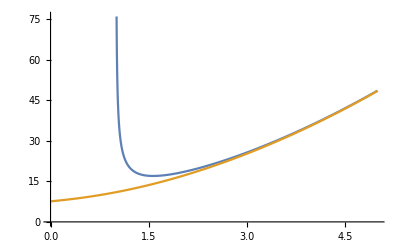

```mathematica
Plot[{(x^3+5 x^2+4x+5)/(√(x^2+2x-3)),√(58+34 x+20 x^2+8 x^3+x^4)},{x,0,5},AxesOrigin->{0,0}]
```

For this problem you could use Reduce or Solve. Each command uses a different syntax for the solutions and Solve warns you that it may not have found all the solutions:

```mathematica
Reduce[{Cos[y] Cos[x Cos[y]],-x Cos[x Cos[y]] Sin[y]}=={0,0},{x,y},Reals]
```

((C[1]|C[2])∈ℤ&&C[1]≤0&&((x≤1/2 (-π+4 π C[1])&&(y==-ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]))||(x≥1/2 (π-4 π C[1])&&(y==-ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]))))||((C[1]|C[2])∈ℤ&&C[1]≥1&&((x≤1/2 (π-4 π C[1])&&(y==-ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]))||(x≥1/2 (-π+4 π C[1])&&(y==-ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]))))||((C[1]|C[2])∈ℤ&&C[1]≤-1&&((x≤1/2 (π+4 π C[1])&&(y==-ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]))||(x≥1/2 (-π-4 π C[1])&&(y==-ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]))))||((C[1]|C[2])∈ℤ&&C[1]≥0&&((x≤1/2 (-π-4 π C[1])&&(y==-ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]))||(x≥1/2 (π+4 π C[1])&&(y==-ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]))))||(C[1]∈ℤ&&x==0&&(y==-π/2+2 π C[1]||y==π/2+2 π C[1]))

```mathematica
Solve[{Cos[y] Cos[x Cos[y]],-x Cos[x Cos[y]] Sin[y]}=={0,0},{x,y},Reals]
```

{{y→ConditionalExpression[-ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2],((C[1]|C[2])∈ℤ&&-π+2 x+4 π C[1]≥0&&C[1]≤0)||((C[1]|C[2])∈ℤ&&-π+2 x+4 π C[1]≤0&&C[1]≥1)||((C[1]|C[2])∈ℤ&&C[1]≥1&&π+2 x-4 π C[1]≥0)||((C[1]|C[2])∈ℤ&&C[1]≤0&&π+2 x-4 π C[1]≤0)]},{y→ConditionalExpression[ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2],((C[1]|C[2])∈ℤ&&-π+2 x+4 π C[1]≥0&&C[1]≤0)||((C[1]|C[2])∈ℤ&&-π+2 x+4 π C[1]≤0&&C[1]≥1)||((C[1]|C[2])∈ℤ&&C[1]≥1&&π+2 x-4 π C[1]≥0)||((C[1]|C[2])∈ℤ&&C[1]≤0&&π+2 x-4 π C[1]≤0)]},{y→ConditionalExpression[-ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2],((C[1]|C[2])∈ℤ&&π+2 x+4 π C[1]≥0&&C[1]≤-1)||((C[1]|C[2])∈ℤ&&π+2 x+4 π C[1]≤0&&C[1]≥0)||((C[1]|C[2])∈ℤ&&C[1]≥0&&-π+2 x-4 π C[1]≥0)||((C[1]|C[2])∈ℤ&&C[1]≤-1&&-π+2 x-4 π C[1]≤0)]},{y→ConditionalExpression[ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2],((C[1]|C[2])∈ℤ&&π+2 x+4 π C[1]≥0&&C[1]≤-1)||((C[1]|C[2])∈ℤ&&π+2 x+4 π C[1]≤0&&C[1]≥0)||((C[1]|C[2])∈ℤ&&C[1]≥0&&-π+2 x-4 π C[1]≥0)||((C[1]|C[2])∈ℤ&&C[1]≤-1&&-π+2 x-4 π C[1]≤0)]},{x→ConditionalExpression[0,C[1]∈ℤ],y→ConditionalExpression[-π/2+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[0,C[1]∈ℤ],y→ConditionalExpression[π/2+2 π C[1],C[1]∈ℤ]}}

The last item in both outputs above gives numerical values for both x and y. This is the collection of discrete solutions. Earlier items express y as a function of x. These are curves. We can rewrite the discrete solutions as follows (we list only a few), and make a visual display:

```mathematica
sols1=Table[{0,-π/2+2 π c},{c,-2,2}]
```

{{0,-(9 π)/2},{0,-(5 π)/2},{0,-π/2},{0,(3 π)/2},{0,(7 π)/2}}

```mathematica
sols2=Table[{0,π/2+ 2π c},{c,-2,2}]
```

{{0,-(7 π)/2},{0,-(3 π)/2},{0,π/2},{0,(5 π)/2},{0,(9 π)/2}}

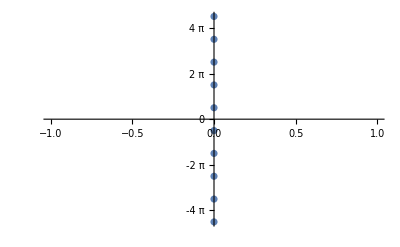

```mathematica
ListPlot[Join[sols1,sols2],Ticks->{None,Range[-4π,4π,π]}]
```

Simply type a list of the equations as the first argument. The solution curves for the first equation appear in blue, while the solution curves for the second equation are (translucent) red. Some curves are solutions to both equations; these appear in purple since the translucent red is laid over the blue in the plot. It is these that are the solutions to the system (and that are algebraically described so elegantly by Reduce). You’ll notice the discrete points from previous part (above) are intersections of red and blue lines in the ContourPlot.

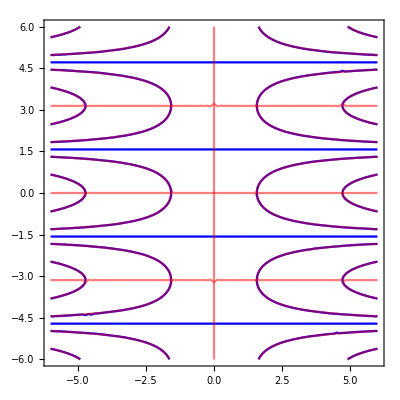

```mathematica
ContourPlot[{Cos[y] Cos[x Cos[y]]==0,-x Cos[x Cos[y]] Sin[y]==0},{x,-6,6},{y,-6,6},ContourStyle->{Blue,Directive[Red,Opacity[.5]]}]
```

```mathematica
Clear[sols1,sols2]
```

Below we show three different ways to enter the both Reduce and Solve commands since each gives a slightly different form of the solution. The first two commands do not restrict the solution set. The other four restrict the solution set to the real numbers. In the third and fourth commands the values for x are requested first, then the values for y. In the last two inputs that order is reversed. The Reduce outputs include more information, are easier to read and don’t include Solve’s ominous red warning note. The ContourPlot shows that the solution set is three lines in the plane. Notice the small break in the vertical line when y = ±1, since these values are excluded from the domain.

```mathematica
Reduce[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{x,y}]
```

(x==0&&-1+y^2≠0)||y==-1/(√3)||y==1/(√3)

```mathematica
Solve[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{x,y}]
```

{{x→0},{y→-1/(√3)},{y→1/(√3)}}

```mathematica
Reduce[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{x,y},Reals]
```

(x<0&&(y==-1/(√3)||y==1/(√3)))||(x==0&&(y<-1||-1<y<1||y>1))||(x>0&&(y==-1/(√3)||y==1/(√3)))

```mathematica
Solve[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{x,y},Reals]
```

{{x→ConditionalExpression[0,-1<y<-1/(√3)||y>1||-1/(√3)<y<1/(√3)||1/(√3)<y<1||y<-1]},{y→-1/(√3)},{y→1/(√3)}}

```mathematica
Reduce[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{y,x},Reals]
```

y==-1/(√3)||y==1/(√3)||((y<-1||-1<y<-1/(√3)||-1/(√3)<y<1/(√3)||1/(√3)<y<1||y>1)&&x==0)

```mathematica
Solve[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{y,x},Reals]
```

{{x→ConditionalExpression[0,-1<y<-1/(√3)||y>1||-1/(√3)<y<1/(√3)||1/(√3)<y<1||y<-1]},{y→-1/(√3)},{y→1/(√3)}}

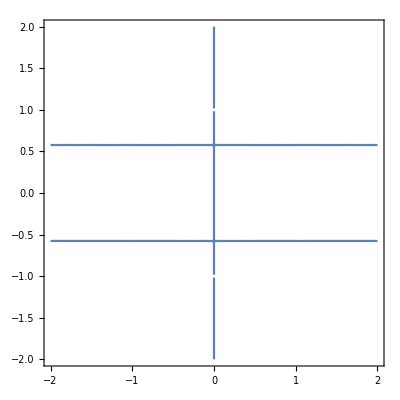

```mathematica
ContourPlot[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{x,-2,2},{y,-2,2}]
```

### Section 4.4

Open the control panel for the slider, and watch the values of c as you move the slider. You’ll find that when c is near 2 the function appears to have exactly two roots (although it will be hard to find the precise point where this occurs using the slider). Input the exact value 2 into the input field below the slider and hit ⌤ to confirm that c=2 is indeed the correct value. Alternately, one could use Reduce or Factor on the polynomial 2-6x+8 x^3.

```mathematica
Reduce[2-6x+8 x^3==0,x]
```

x==-1||x==1/2

```mathematica
Factor[2-6x+8 x^3]
```

2 (1+x) (-1+2 x)^2

Since Surd[x,5] gives the real 5th root of x, we square this to get the desired function. f(32)=32^(2/5)=(32^(1/5))^2=2^2=4. This is consistent with the plot:

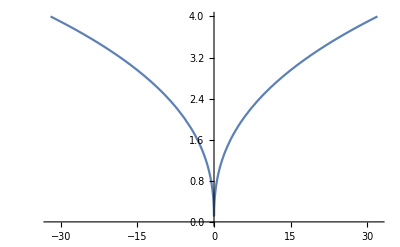

```mathematica
Plot[Surd[x,5]^2,{x,-32,32}]
```

In this case adding the option setting Quartics → True does not effect the output.

```mathematica
Reduce[x^4-x==0,x]
```

x==0||x==1||x==-(-1)^(1/3)||x==(-1)^(2/3)

```mathematica
Reduce[x^4-x==0,x,Quartics->True]
```

x==0||x==1||x==-(-1)^(1/3)||x==(-1)^(2/3)

Here are the real roots:

```mathematica
Reduce[x^4-x==0,x,Reals]
```

x==0||x==1

Just as a real number may be expressed in such a way that an ⅈ appears (for instance -1=ⅈ^2), a complex number may be expressed in such a way that no ⅈ appears. The command ComplexExpand can be used to reformulate this type of complex number into the standard form a+bⅈ. When applied to the two non-real roots above, we get:

```mathematica
{-(-1)^(1/3),(-1)^(2/3)}//ComplexExpand
```

{-1/2-(ⅈ √3)/2,-1/2+(ⅈ √3)/2}

The option setting Quartics → True does effect the output for this equation. We display only the first root to save space, but note that adding the Quartics → True option affects the order in which the roots are displayed. As before, there are two real and two non-real roots, although there are no ⅈ’s appearing in any of the four roots. As before, ComplexExpand can be used to put the non-real roots (such as the one shown below) into standard a+bⅈ form:

```mathematica
Reduce[x^4-x-1==0,x]
```

x==Root-0.724Root[-1-#1+#1^4&,1]-0.7244919590005157||x==Root1.22Root[-1-#1+#1^4&,2]1.2207440846057596||x==Root-0.248-1.03 ⅈRoot[-1-#1+#1^4&,3]-0.24812606280262192||x==Root-0.248+1.03 ⅈRoot[-1-#1+#1^4&,4]-0.24812606280262192

```mathematica
Reduce[x^4-x-1==0,x,Quartics->True]⟦1⟧
```

x==-1/2 √(-4 (2/(3 (9+√849)))^(1/3)+(1/2 (9+√849))^(1/3)/3^(2/3))-1/2 √(4 (2/(3 (9+√849)))^(1/3)-(1/2 (9+√849))^(1/3)/3^(2/3)-2/(√(-4 (2/(3 (9+√849)))^(1/3)+(1/2 (9+√849))^(1/3)/3^(2/3))))

```mathematica
Simplify[ComplexExpand[Reduce[x^4-x-1==0,x,Quartics->True]⟦1⟧]]
```

x==-1/(2 6^(1/3))(√(-8 (3/(9+√849))^(1/3)+(2 (9+√849))^(1/3))+ⅈ √(-8 (3/(9+√849))^(1/3)+(2 (9+√849))^(1/3)+12/(√(-8 (3/(9+√849))^(1/3)+(2 (9+√849))^(1/3)))))

The polynomial (x-2)^3 has degree three, so it has three linear factors. Each gives a root of the polynomial. In this case all of the three linear factors are identical: (x-2). So there is only one root. But because there are three factors, the root associated with each is reported.

This is fun to play with. It nicely illustrates a general fact: the complex roots of a real polynomial come in conjugate pairs. If one root is a+bⅈ then another will be a-bⅈ. In geometric terms, the roots are symmetric with respect to the x-axis. Note that we set the PlotRange to 2 (not 4), as all five roots will be contained in this window.

```mathematica
Manipulate[Graphics[{Directive[Red,PointSize[.02]],Point[{Re[x],Im[x]}]/.NSolve[x^5+a x^4+b x^3+c x^2+d x+e==0,x]},Axes->True,PlotRange->2],
{{a,0},-2,2},{{b,0},-2,2},{{c,0},-2,2},{{d,1},-2,2},{{e,-1},-2,2}]
```

Note that the Graphics option setting PlotRange → 1 keeps the image stable as n is changed.

```mathematica
Manipulate[Graphics[{
{Thick,Blue,Line[{{0,0},{Re[x],Im[x]}}]/.NSolve[x^n+1==0,x]},
{Red,PointSize[.03],Point[{Re[x],Im[x]}]/.NSolve[x^n+1==0,x]}},Axes->True,AxesLabel->{"real","imaginary"},PlotRange->1,PlotLabel->"n roots of -1"],{{n,7},Range[10],ControlType->SetterBar}]
```

This is very fun:

```mathematica
Manipulate[
Graphics[Line[Table[{Re[z],Im[z]},{z,Table[(-k)^x,{x,-4,0,.01}]}]],Axes->True,PlotRange->2],
{{k,2},.1,4}]
```

### Section 4.5

Factor the numerator and denominator of (-6-7 x-x^2+x^3+x^4)/(-2-x+x^2). We see that both roots of the denominator are also roots of the numerator. This rational function is the same as 3+2x+x^2 except that the rational function has two holes in its graph (barely visible here), at x=-1 and at x=2.

```mathematica
Factor[{-6-7 x-x^2+x^3+x^4,-2-x+x^2}]
```

{(-2+x) (1+x) (3+2 x+x^2),(-2+x) (1+x)}

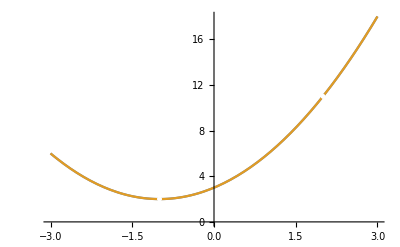

```mathematica
Plot[{(-6-7 x-x^2+x^3+x^4)/(-2-x+x^2),x^2+2x+3},{x,-3,3},Exclusions->{-2-x+x^2==0},ExclusionsStyle->{Dotted,White},AxesOrigin->{0,0}]
```

The rational function (-6-7 x-x^2+x^3+x^4)/(-4-x+x^2) has the same numerator as the function in the previous exercise, so it factors as (x-2)(x+1)(x^2+2x+3). The quadratic factor has no real roots since b^2-4a c<0. Hence the numerator has roots only at x=-1 and x=2. The denominator has two real roots (since b^2-4a c>0), but neither is at -1 or 2. Hence the rational function has vertical asymptotes at the roots of the denominator, x=1/2(1±√17), as indicated by the first output below. Long division reveals that the rational function is asymptotic to the quadratic 5+2x+x^2 as x approaches ±∞. The graph bears this out.

```mathematica
Reduce[-4-x+x^2==0,x]
```

x==1/2 (1-√17)||x==1/2 (1+√17)

```mathematica
PolynomialQuotient[-6-7 x-x^2+x^3+x^4,-4-x+x^2,x]
```

5+2 x+x^2

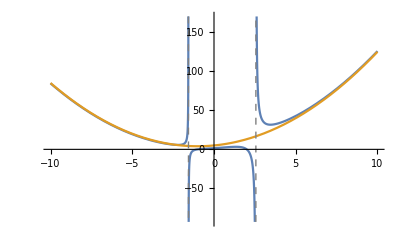

```mathematica
Plot[{(-6-7 x-x^2+x^3+x^4)/(-4-x+x^2),5+2x+x^2},{x,-10,10},Exclusions->{-4-x+x^2==0},ExclusionsStyle->Directive[Dashed,Gray]]
```

### Section 4.6

A Table is useful for examining many expressions together. See Chapter 8.4, exercise 8 for a similar table, but with more nuanced formatting.

```mathematica
Clear[t];
Table[TrigExpand[Sin[n t]],{n,1,7}]//Column
```

Sin[t]
2 Cos[t] Sin[t]
3 Cos[t]^2 Sin[t]-Sin[t]^3
4 Cos[t]^3 Sin[t]-4 Cos[t] Sin[t]^3
5 Cos[t]^4 Sin[t]-10 Cos[t]^2 Sin[t]^3+Sin[t]^5
6 Cos[t]^5 Sin[t]-20 Cos[t]^3 Sin[t]^3+6 Cos[t] Sin[t]^5
7 Cos[t]^6 Sin[t]-35 Cos[t]^4 Sin[t]^3+21 Cos[t]^2 Sin[t]^5-Sin[t]^7

The Manipulate below shows the graphs of the two expressions coincide. The first is blue and the second is dashed yellow so both can be seen at the same time. The other curves show (sin(a t))/(2sin(t)) and (sin((2-a)t))/(2sin(t)) and how their values combine for various values of a. The identity is equivalent to sin(a t)+sin((2-a)t)=2cos((1-a)t)sin(t). We can use TrigFactor and then Simplify to change the expression on the left of the equal sign into the expression on the right.

```mathematica
Manipulate[Plot[{(Sin[a t]+Sin[(2-a)t])/(2Sin[t]),Cos[(1-a) t],Sin[a t]/(2Sin[t]),Sin[(2-a)t]/(2Sin[t])},{t,0,8π},PlotRange->2,PlotStyle->{Blue,Dashed,Automatic,Automatic}],{{a,.3},0,2}]
```

```mathematica
Clear[a,t];
TrigFactor[Sin[a t]+Sin[(2-a)t]]
```

2 Cos[1/2 (2-a) t-(a t)/2] Sin[1/2 (2-a) t+(a t)/2]

```mathematica
2 Cos[Simplify[1/2 (2-a) t-(a t)/2]] Sin[Simplify[1/2 (2-a) t+(a t)/2]]
```

2 Cos[t-a t] Sin[t]

We first derive a quadruple angle formula for the cosine function; to get it into a nice form we replace both sin^2(a) and sin^4(a) using the standard relation sin^2(a)+cos^2(a)=1. Taking a=π/12, (so that 4a=π/3), we see that cos(4a)=1/2. Our quadruple angle formula then gives that cos(π/12) is a root of 16 x^4-16 x^2+1.

```mathematica
Cos[4a]//TrigExpand
```

Cos[a]^4-6 Cos[a]^2 Sin[a]^2+Sin[a]^4

```mathematica
(Cos[4a]//TrigExpand)/.{Sin[a]^2->1-Cos[a]^2,Sin[a]^4->(1-Cos[a]^2)^2}//Expand
```

1-8 Cos[a]^2+8 Cos[a]^4

```mathematica
16 x^4-16 x^2+1/.x->Cos[π/12]//Simplify
```

0

### Section 4.7

First we sketch the two curves y=1-x^2 and y=sin x in the x-y plane. You will find that neither Solve, nor NSolve, nor Reduce is capable of solving the equation 1-x^2=sin x, so we resort to FindRoot, which will approximate the roots one at a time when given an initial guess. The Plot allows us to make educated initial guesses of x=-1.4 on the left, and x=0.6 on the right.

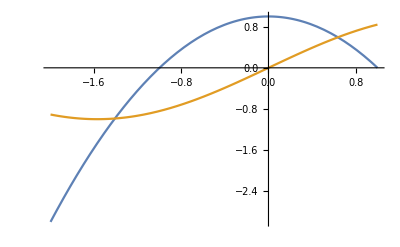

```mathematica
Plot[{1-x^2,Sin[x]},{x,-2,1}]
```

```mathematica
x/.{FindRoot[1-x^2==Sin[x],{x,-1.4}],FindRoot[1-x^2==Sin[x],{x,.6}]}
```

{-1.40962,0.636733}

First we sketch the two curves y=ⅇ^(-x^2) and y=sin x in the x-y plane. You will find that neither Solve, nor NSolve, nor Reduce is capable of solving the equation sin x=ⅇ^(-x^2), so we resort to FindRoot, which will approximate the roots one at a time when given an initial guess. The Plot allows us to make educated initial guesses of x=-3 on the left, and x=0.75 and x=3 on the right.

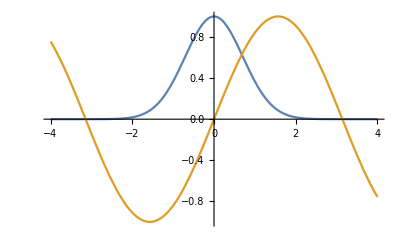

```mathematica
Plot[{ⅇ^(-x^2),Sin[x]},{x,-4,4}]
```

```mathematica
x/.Table[FindRoot[ⅇ^(-x^2)==Sin[x],{x,x0}],{x0,{-3,.75,3}}]
```

{-3.14164,0.680598,3.14154}

No. ⅇ^(-π^2)>0, while sin π=0. Resolve can be used to verify or in some cases refute an equation, as it is below. However there is a number x just a tad smaller than π for which ⅇ^(-x^2)=sin x (see the rightmost solution above). This equation is in a sense almost true!

```mathematica
ⅇ^(-π^2)==Sin[π]
```

False

### Section 4.8

Let n denote time in months, and let s[n] denote the amount still owed to the lender after n months. Then s[0]=30000, and since (.07)/12 is the monthly interest rate and the monthly payment is p, we have s[n]=s[n-1]+(.07)/12 s[n-1]-p=(1+(.07)/12)s[n-1]-p. As it’s a five-year loan, we also have that s[60]=0.

Now there is no simple means for solving a difference equation like this for a constant p using RSolve. However, we can do something that is more general: solve a system of two difference equations. That is, we may treat p as a function of n as well. Since it is constant, it satisfies the trivial difference equation p[n]=p[n-1]. Following the calculations below we find that the monthly payment is $594.04.

```mathematica
Clear[sols,s,p,n];
sols=RSolve[{s[n]==(1+(.07)/12)s[n-1]-p[n],s[0]==30000,s[60]==0,p[n]==p[n-1]},{p,s},n]
```

{{p→Function[{n},594.036],s→Function[{n},-71834.7 (-1.41763+1. 1.00583^n)]}}

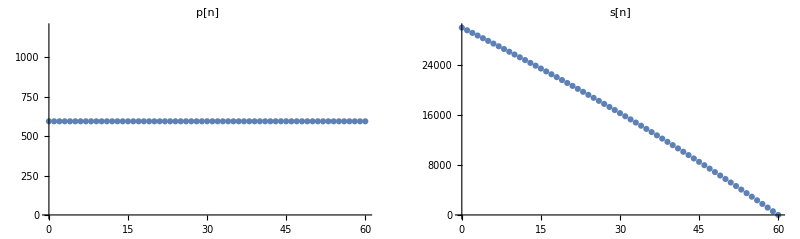

```mathematica
GraphicsRow[{ListPlot[Table[{n,p[n]/.sols⟦1⟧},{n,0,60}],PlotLabel->"p[n]"],ListPlot[Table[{n,s[n]/.sols⟦1⟧},{n,0,60}],PlotLabel->"s[n]"]}]
```

```mathematica
Clear[sols,s,p,n];
```

Use the result above to define the requisite quantities. The table below is accurate for the first 59 months. The final payment will be reduced by 29 cents, since paying the full amount would result in that overpayment.

```mathematica
Clear[p,s,n];
p=594.04;
s[n_Integer]:=Piecewise[{{s[0]=30000, n==0}, {s[n]=(1+(.07)/12)s[n-1]-p, n>0}}]
```

```mathematica
Text@Grid[Prepend[Table[{n,s[n],(.07)/12 s[n-1],p-(.07)/12 s[n-1],p},{n,1,60}],{"month","remaining principal","payment: interest","payment: principal", "payment"}],Dividers->Gray]
```

month | remaining principal | payment: interest | payment: principal | payment
1 | 29581. | 175. | 419.04 | 594.04
2 | 29159.5 | 172.556 | 421.484 | 594.04
3 | 28735.5 | 170.097 | 423.943 | 594.04
4 | 28309.1 | 167.624 | 426.416 | 594.04
5 | 27880.2 | 165.137 | 428.903 | 594.04
6 | 27448.8 | 162.635 | 431.405 | 594.04
7 | 27014.9 | 160.118 | 433.922 | 594.04
8 | 26578.4 | 157.587 | 436.453 | 594.04
9 | 26139.4 | 155.041 | 438.999 | 594.04
10 | 25697.9 | 152.48 | 441.56 | 594.04
11 | 25253.7 | 149.904 | 444.136 | 594.04
12 | 24807. | 147.313 | 446.727 | 594.04
13 | 24357.7 | 144.708 | 449.332 | 594.04
14 | 23905.7 | 142.086 | 451.954 | 594.04
15 | 23451.1 | 139.45 | 454.59 | 594.04
16 | 22993.9 | 136.798 | 457.242 | 594.04
17 | 22534. | 134.131 | 459.909 | 594.04
18 | 22071.4 | 131.448 | 462.592 | 594.04
19 | 21606.1 | 128.75 | 465.29 | 594.04
20 | 21138.1 | 126.036 | 468.004 | 594.04
21 | 20667.4 | 123.306 | 470.734 | 594.04
22 | 20193.9 | 120.56 | 473.48 | 594.04
23 | 19717.6 | 117.798 | 476.242 | 594.04
24 | 19238.6 | 115.02 | 479.02 | 594.04
25 | 18756.8 | 112.225 | 481.815 | 594.04
26 | 18272.2 | 109.415 | 484.625 | 594.04
27 | 17784.7 | 106.588 | 487.452 | 594.04
28 | 17294.4 | 103.744 | 490.296 | 594.04
29 | 16801.3 | 100.884 | 493.156 | 594.04
30 | 16305.2 | 98.0074 | 496.033 | 594.04
31 | 15806.3 | 95.1139 | 498.926 | 594.04
32 | 15304.5 | 92.2035 | 501.836 | 594.04
33 | 14799.7 | 89.2761 | 504.764 | 594.04
34 | 14292. | 86.3317 | 507.708 | 594.04
35 | 13781.3 | 83.3701 | 510.67 | 594.04
36 | 13267.7 | 80.3911 | 513.649 | 594.04
37 | 12751. | 77.3949 | 516.645 | 594.04
38 | 12231.4 | 74.3811 | 519.659 | 594.04
39 | 11708.7 | 71.3498 | 522.69 | 594.04
40 | 11183. | 68.3007 | 525.739 | 594.04
41 | 10654.2 | 65.2339 | 528.806 | 594.04
42 | 10122.3 | 62.1492 | 531.891 | 594.04
43 | 9587.27 | 59.0465 | 534.993 | 594.04
44 | 9049.15 | 55.9257 | 538.114 | 594.04
45 | 8507.9 | 52.7867 | 541.253 | 594.04
46 | 7963.49 | 49.6294 | 544.411 | 594.04
47 | 7415.9 | 46.4537 | 547.586 | 594.04
48 | 6865.12 | 43.2594 | 550.781 | 594.04
49 | 6311.13 | 40.0465 | 553.993 | 594.04
50 | 5753.9 | 36.8149 | 557.225 | 594.04
51 | 5193.43 | 33.5644 | 560.476 | 594.04
52 | 4629.68 | 30.295 | 563.745 | 594.04
53 | 4062.65 | 27.0065 | 567.034 | 594.04
54 | 3492.31 | 23.6988 | 570.341 | 594.04
55 | 2918.64 | 20.3718 | 573.668 | 594.04
56 | 2341.63 | 17.0254 | 577.015 | 594.04
57 | 1761.24 | 13.6595 | 580.381 | 594.04
58 | 1177.48 | 10.2739 | 583.766 | 594.04
59 | 590.307 | 6.86862 | 587.171 | 594.04
60 | -0.289507 | 3.44346 | 590.597 | 594.04

```mathematica
Clear[p,s]
```

We use RSolve to find the function v(n) that gives the car’s value after n years. Then using Reduce we find the precise number of years (roughly twelve and a half) until the car reaches $8000 in value.

```mathematica
Clear[v,n];
RSolve[{v[n]==9/10 v[n-1],v[0]==30000},v[n],n]
```

{{v[n]→3^(1+2 n) 10^(4-n)}}

```mathematica
30000(9/10)^n//Expand
```

3^(1+2 n) 10^(4-n)

```mathematica
Reduce[30000(9/10)^n==8000,n,Reals]
```

n==(-2 Log[2]+Log[3]+Log[5])/(Log[2]-2 Log[3]+Log[5])

```mathematica
N[%]
```

n==12.5451

### Section 4.9

Even though this system has one easy solution (at the origin), neither Solve nor NSolve can solve this system. Using FindRoot we are able to approximate all four solutions shown in the graph. Reduce can also be used but we need to calculate the corresponding y-values.

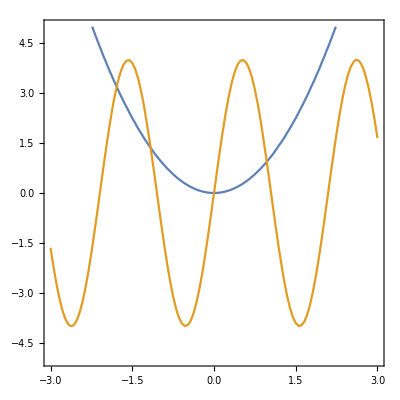

```mathematica
ContourPlot[{y==x^2,y==4Sin[3x]},{x,-3,3},{y,-5,5}]
```

```mathematica
Solve[{y==x^2,y==4Sin[3x]}]
```

Solve[{y==x^2,y==4 Sin[3 x]}]

```mathematica
NSolve[{y==x^2,y==4Sin[3x]},{x,y}]
```

NSolve[{y==x^2,y==4 Sin[3 x]},{x,y}]

```mathematica
FindRoot[{y==x^2,y==4Sin[3x]},{x,0},{y,0}]
```

{x→0.,y→0.}

```mathematica
FindRoot[{y==x^2,y==4Sin[3x]},{x,1},{y,1}]
```

{x→0.968326,y→0.937655}

```mathematica
FindRoot[{y==x^2,y==4Sin[3x]},{x,-1},{y,1}]
```

{x→-1.16197,y→1.35016}

```mathematica
FindRoot[{y==x^2,y==4Sin[3x]},{x,-2},{y,3}]
```

{x→-1.78648,y→3.19149}

```mathematica
Reduce[{y==x^2,y==4Sin[3x]},{x,y},Reals]
```

(x==Root-1.79Root[{-4 Sin[3 #1]+#1^2&,-1.7864753065779236165}]-1.7864753065779235||x==Root-1.16Root[{-4 Sin[3 #1]+#1^2&,-1.1619652741819767893}]-1.1619652741819768||x==0||x==Root0.968Root[{-4 Sin[3 #1]+#1^2&,0.96832574842786382575}]0.9683257484278638)&&y==x^2

```mathematica
N[%]
```

(x==-1.78648||x==-1.16197||x==0.||x==0.968326)&&y==x^2

```mathematica
4Sin[3x]/.x->{-1.7864753065,-1.1619652741,0,0.9683257484}
```

{3.19149,1.35016,0,0.937655}